# Pendekatan Kuadrat Terkecil Terbobot Bulan Mulya Utama & Chalista Divia Maharani

### Kasus Diskrit

Tentukan polinomial pendekatan kuadrat terkecil yaitu polinomial berderajat satu sampai lima pada 55 data di bawah dengan bobot wi = 1; i = 0, 1, 2, · · · , 54.

```mathematica
xi={0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54}
fi={1.35,1.38,1.45,1.47,1.52,1.56,1.60,1.63,1.65,1.69,1.71,1.74,1.77,1.79,1.82,1.84,1.90,1.93,1.98,2.01,2.04,2.07,2.11,2.14,2.16,2.22,2.28,2.34,2.39,2.45,2.48,2.54,2.59,2.66,2.71,2.77,2.83,2.95,3.12,3.21,3.32,3.40,3.50,3.56,3.61,3.65,3.69,3.72,3.75,3.80,3.84,3.88,3.92,4.03,4.07}
wi=1
```

```mathematica
data=Transpose[{xi,fi}]
```

{{0,1.35},{1,1.38},{2,1.45},{3,1.47},{4,1.52},{5,1.56},{6,1.6},{7,1.63},{8,1.65},{9,1.69},{10,1.71},{11,1.74},{12,1.77},{13,1.79},{14,1.82},{15,1.84},{16,1.9},{17,1.93},{18,1.98},{19,2.01},{20,2.04},{21,2.07},{22,2.11},{23,2.14},{24,2.16},{25,2.22},{26,2.28},{27,2.34},{28,2.39},{29,2.45},{30,2.48},{31,2.54},{32,2.59},{33,2.66},{34,2.71},{35,2.77},{36,2.83},{37,2.95},{38,3.12},{39,3.21},{40,3.32},{41,3.4},{42,3.5},{43,3.56},{44,3.61},{45,3.65},{46,3.69},{47,3.72},{48,3.75},{49,3.8},{50,3.84},{51,3.88},{52,3.92},{53,4.03},{54,4.07}}

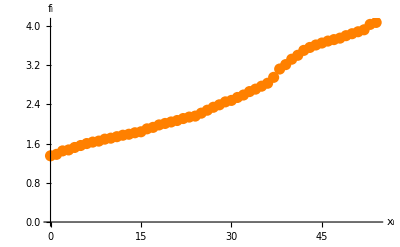

```mathematica
PlotData=ListPlot[data,PlotStyle->{Orange,PointSize[0.02]},AxesLabel->{"x_i","f_i"}]
```

Polinomial Berderajat Satu

```mathematica
LeastSquares[({{∑_(i=0)^54 wi, ∑_(i=0)^0 wi×xi}, {∑_(i=0)^0 wi×xi, ∑_(i=0)^0 wi×xi^2}}),({{∑_(i=0)^0 wi×fi}, {∑_(i=0)^0 wi×fi×xi^1}})]
```

```mathematica
a=∑_(i=0)^54 wi
```

55

```mathematica
b=Total[∑_(i=0)^0 wi×xi]
```

1485

```mathematica
c=Total[∑_(i=0)^0 wi×xi]
```

1485

```mathematica
d=Total[∑_(i=0)^0 wi×xi^2]
```

53955

```mathematica
e=Total[∑_(i=0)^0 wi×fi]
```

139.59

```mathematica
f=Total[∑_(i=0)^0 wi×fi×xi^1]
```

4491.45

```mathematica
LeastSquares[({{a, b}, {c, d}}),({{e}, {f}})]
```

{{1.13049},{0.0521299}}

Diperoleh a_0=1.13049 dan a_1=0.0521299 sehingga diperoleh polinomial berderajat 1 yaitu P_1(x)=1.13049+0.0521299x.

```mathematica
P1[x_]=1.13049+0.0521299x
```

1.13049+0.0521299 x

Berikut merupakan grafik polinomial pendek atan berderajat satu.

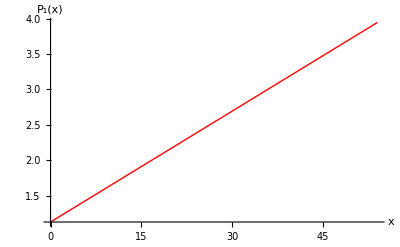

```mathematica
PlotP1=Plot[{P1[x]},{x,0,54},AxesLabel-> {"x","P_1(x)"},PlotStyle->{{Red,Thick}}]
```

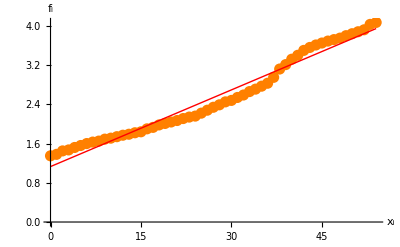

```mathematica
Show[{PlotData,PlotP1}]
```

```mathematica
fP1 = P1[xi]
```

{1.13049,1.18262,1.23475,1.28688,1.33901,1.39114,1.44327,1.4954,1.54753,1.59966,1.65179,1.70392,1.75605,1.80818,1.86031,1.91244,1.96457,2.0167,2.06883,2.12096,2.17309,2.22522,2.27735,2.32948,2.38161,2.43374,2.48587,2.538,2.59013,2.64226,2.69439,2.74652,2.79865,2.85078,2.90291,2.95504,3.00717,3.0593,3.11143,3.16356,3.21569,3.26782,3.31995,3.37208,3.42421,3.47634,3.52847,3.5806,3.63273,3.68486,3.73699,3.78911,3.84124,3.89337,3.9455}

```mathematica
ErorP1=fi-fP1
```

{0.21951,0.19738,0.21525,0.18312,0.18099,0.168861,0.156731,0.134601,0.102471,0.0903409,0.058211,0.0360811,0.0139512,-0.0181787,-0.0403086,-0.0724385,-0.0645684,-0.0866983,-0.0888282,-0.110958,-0.133088,-0.155218,-0.167348,-0.189478,-0.221608,-0.213737,-0.205867,-0.197997,-0.200127,-0.192257,-0.214387,-0.206517,-0.208647,-0.190777,-0.192907,-0.185037,-0.177166,-0.109296,0.0085738,0.0464439,0.104314,0.132184,0.180054,0.187924,0.185794,0.173665,0.161535,0.139405,0.117275,0.115145,0.103015,0.0908851,0.0787552,0.136625,0.124495}

Berikut merupakan grafik distribusi eror dari polinomial pendekatan berderajat satu.

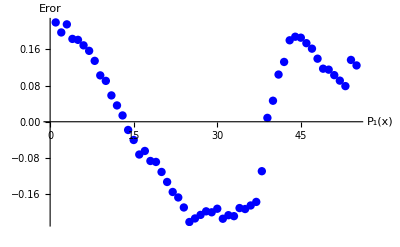

```mathematica
ploter1=ListPlot[ErorP1,PlotRange->All,PlotStyle->{Blue,PointSize[0.015]},AxesLabel->{"P_1(x)","Eror"}]
```

```mathematica
EP1=Total[wi(ErorP1)^2]
```

1.27081

Diperoleh nilai E (eror) dari polinomial pendekatan berderajat satu adalah E(P_1) = 1.27081.

Polinomial Berderajat Dua

```mathematica
LeastSquares[({{∑_(i=0)^54 wi, ∑_(i=0)^0 wi×xi, ∑_(i=0)^0 wi×xi^2}, {∑_(i=0)^0 wi×xi, ∑_(i=0)^0 wi×xi^2, ∑_(i=0)^0 wi×xi^3}, {∑_(i=0)^0 wi×xi^2, ∑_(i=0)^0 wi×xi^3, ∑_(i=0)^0 wi×xi^4}}),({{∑_(i=0)^0 wi×fi}, {∑_(i=0)^0 wi×fi×xi^1}, {∑_(i=0)^0 wi×fi×xi^2}})]
```

```mathematica
∑_(i=0)^54 wi
```

55

```mathematica
Total[∑_(i=0)^0 wi×xi]
```

1485

```mathematica
Total[∑_(i=0)^0 wi×xi^2]
```

53955

```mathematica
Total[∑_(i=0)^0 wi×xi^3]
```

2205225

```mathematica
Total[∑_(i=0)^0 wi×xi^4]
```

96137019

```mathematica
Total[∑_(i=0)^0 wi×fi]
```

139.59

```mathematica
Total[∑_(i=0)^0 wi×fi×xi^1]
```

4491.45

```mathematica
Total[∑_(i=0)^0 wi×fi×xi^2]
```

177555.

```mathematica
LeastSquares[({{55, 1485, 53955}, {1485, 53955, 2205225}, {53955, 2205225, 96137019}}),({{139.59}, {4491.45}, {177555}})]
```

{{1.4041},{0.0211558},{0.000573593}}

```mathematica
Flatten[{{1.4041},{0.0211558},{0.000573593}}]
```

{1.4041,0.0211558,0.000573593}

Diperoleh a_0=1.4041, a_1=0.0211558, dan a_2=0.000573593 sehingga diperoleh polinomial berderajat 2 yaitu P_2(x)=1.4041+0.0211558x+0.000573593 x^2.

```mathematica
P2[x_]=1.4041+0.0211558x+0.000573593 x^2
```

1.4041+0.0211558 x+0.000573593 x^2

Berikut merupakan grafik polinomial pendekatan berderajat dua.

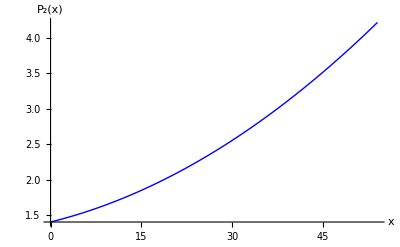

```mathematica
PlotP2=Plot[{P2[x]},{x,0,54},AxesLabel-> {"x","P_2(x)"},PlotStyle->{{Blue,Thick}}]
```

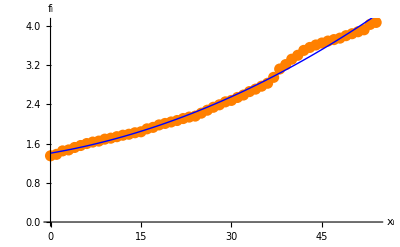

```mathematica
Show[{PlotData,PlotP2}]
```

```mathematica
fP2 = P2[xi]
```

{1.4041,1.42583,1.44871,1.47273,1.4979,1.52422,1.55168,1.5803,1.61006,1.64096,1.67302,1.70622,1.74057,1.77606,1.81271,1.8505,1.88943,1.92952,1.97075,2.01313,2.05665,2.10133,2.14715,2.19411,2.24223,2.29149,2.3419,2.39346,2.44616,2.50001,2.55501,2.61115,2.66844,2.72688,2.78647,2.8472,2.90909,2.97211,3.03629,3.10161,3.16808,3.2357,3.30446,3.37437,3.44543,3.51764,3.59099,3.66549,3.74114,3.81793,3.89587,3.97496,4.0552,4.13658,4.21911}

```mathematica
ErorP2=fi-fP2
```

{-0.0541,-0.0458294,0.00129403,-0.00272974,0.0220993,0.0357812,0.0483159,0.0497033,0.0399436,0.0490368,0.0369827,0.0337814,0.029433,0.0139374,0.00729457,-0.0104954,0.0105674,0.000483023,0.00925147,-0.00312727,-0.0166532,-0.0313263,-0.0371466,-0.0541141,-0.0822288,-0.0714906,-0.0618997,-0.0534559,-0.0561593,-0.0500099,-0.0750077,-0.0711527,-0.0784448,-0.0668842,-0.0764707,-0.0772044,-0.0790853,-0.0221134,0.0837113,0.108389,0.151919,0.164302,0.195538,0.185627,0.164569,0.132363,0.0990104,0.0545105,0.00886333,-0.017931,-0.0558725,-0.0949612,-0.135197,-0.10658,-0.14911}

Berikut merupakan grafik distribusi eror dari polinomial pendekatan berderajat dua.

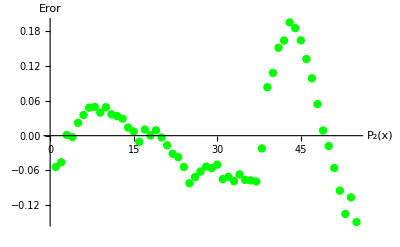

```mathematica
ploter2=ListPlot[ErorP2,PlotRange->All,PlotStyle->{Green,PointSize[0.015]},AxesLabel->{"P_2(x)","Eror"}]
```

```mathematica
EP2=Total[wi(ErorP2)^2]
```

0.352512

Diperoleh nilai E (eror) dari polinomial pendekatan berderajat dua adalah E(P_2) = 0.352512.

Polinomial Berderajat Tiga

```mathematica
LeastSquares[({{∑_(i=0)^54 wi, ∑_(i=0)^0 wi×xi, ∑_(i=0)^0 wi×xi^2, ∑_(i=0)^0 wi×xi^3}, {∑_(i=0)^0 wi×xi, ∑_(i=0)^0 wi×xi^2, ∑_(i=0)^0 wi×xi^3, ∑_(i=0)^0 wi×xi^4}, {∑_(i=0)^0 wi×xi^2, ∑_(i=0)^0 wi×xi^3, ∑_(i=0)^0 wi×xi^4, ∑_(i=0)^0 wi×xi^5}, {∑_(i=0)^0 wi×xi^3, ∑_(i=0)^0 wi×xi^4, ∑_(i=0)^0 wi×xi^5, ∑_(i=0)^0 wi×xi^6}}),({{∑_(i=0)^0 wi×fi}, {∑_(i=0)^0 wi×fi×xi^1}, {∑_(i=0)^0 wi×fi×xi^2}, {∑_(i=0)^0 wi×fi×xi^3}})]
```

```mathematica
Total[∑_(i=0)^0 wi×xi^5]
```

4365610425

```mathematica
Total[∑_(i=0)^0 wi×xi^6]
```

203902041915

```mathematica
Total[∑_(i=0)^0 wi×fi×xi^3]
```

7.62967×10^6

```mathematica
LeastSquares[({{55, 1485, 53955, 2205225}, {1485, 53955, 2205225, 96137019}, {53955, 2205225, 96137019, 4365610425}, {2205225, 96137019, 4365610425, 203902E+11}}),({{139.59}, {4491.45}, {177555}, {7629668}})]
```

{{1.40393},{0.0211953},{0.00057175},{2.27497×10^-8}}

```mathematica
Flatten[{{1.40393},{0.0211953},{0.00057175},{2.27497×10^-8}}]
```

{1.40393,0.0211953,0.00057175,2.27497×10^-8}

Diperoleh a_0=1.40393, a_1=0.0211953, a_2=0.00057175, dan a_3=2.27497×10^-8 sehingga diperoleh polinomial berderajat 3 yaitu P_3(x)=1.40393+0.0211953x+0.00057175 x^2+2.27497×10^-8 x^3.

```mathematica
P3[x_]=1.40393+0.0211953 x+0.00057175 x^2+2.274971358532534×10^-8 x^3
```

1.40393+0.0211953 x+0.00057175 x^2+2.27497×10^-8 x^3

Berikut merupakan grafik polinomial pendekatan berderajat tiga.

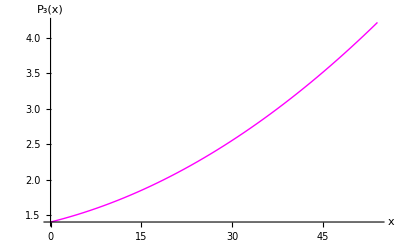

```mathematica
PlotP3=Plot[{P3[x]},{x,0,54},AxesLabel-> {"x","P_3(x)"},PlotStyle->{{Magenta,Thick}}]
```

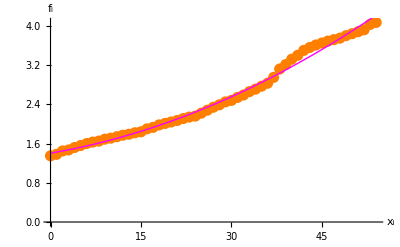

```mathematica
Show[{PlotData,PlotP3}]
```

```mathematica
fP3 = P3[xi]
```

{1.40393,1.4257,1.44861,1.47266,1.49786,1.5242,1.55169,1.58032,1.6101,1.64102,1.67308,1.70629,1.74064,1.77614,1.81279,1.85058,1.88952,1.9296,1.97083,2.0132,2.05672,2.10138,2.1472,2.19415,2.24226,2.29151,2.34191,2.39346,2.44615,2.49999,2.55498,2.61111,2.6684,2.72683,2.78641,2.84713,2.90901,2.97203,3.03621,3.10153,3.168,3.23562,3.30439,3.3743,3.44537,3.51759,3.59095,3.66547,3.74113,3.81795,3.89591,3.97503,4.0553,4.13671,4.21928}

```mathematica
ErorP3=fi-fP3
```

{-0.05393,-0.0456971,0.00139222,-0.00266226,0.0221393,0.0357969,0.0483103,0.0496793,0.039904,0.048984,0.0369193,0.0337097,0.0293551,0.0138554,0.00721037,-0.01058,0.010484,0.000402381,0.00917492,-0.00319849,-0.016718,-0.0313837,-0.0371958,-0.0541544,-0.0822597,-0.0715117,-0.0619106,-0.0534566,-0.0561498,-0.0499903,-0.0749782,-0.0711138,-0.0783971,-0.0668282,-0.0764074,-0.0771346,-0.0790102,-0.0220342,0.0837933,0.108472,0.152002,0.164383,0.195615,0.185698,0.164631,0.132415,0.0990488,0.0545332,0.00886766,-0.0179479,-0.0559137,-0.0950298,-0.135296,-0.106714,-0.149281}

Berikut merupakan grafik distribusi eror dari polinomial pendekatan berderajat tiga.

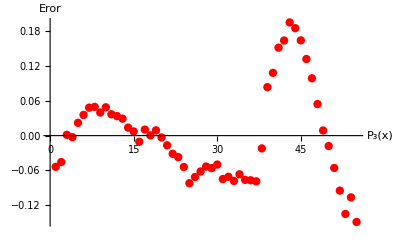

```mathematica
ploter3=ListPlot[ErorP3,PlotRange->All,PlotStyle->{Red,PointSize[0.015]},AxesLabel->{"P_3(x)","Eror"}]
```

```mathematica
EP3=Total[wi(ErorP3)^2]
```

0.352723

Diperoleh nilai E (eror) dari polinomial pendekatan berderajat dua adalah E(P_3) = 0.352723.

Polinomial Berderajat Empat

```mathematica
LeastSquares[({{∑_(i=0)^54 wi, ∑_(i=0)^0 wi×xi, ∑_(i=0)^0 wi×xi^2, ∑_(i=0)^0 wi×xi^3, ∑_(i=0)^0 wi×xi^4}, {∑_(i=0)^0 wi×xi, ∑_(i=0)^0 wi×xi^2, ∑_(i=0)^0 wi×xi^3, ∑_(i=0)^0 wi×xi^4, ∑_(i=0)^0 wi×xi^5}, {∑_(i=0)^0 wi×xi^2, ∑_(i=0)^0 wi×xi^3, ∑_(i=0)^0 wi×xi^4, ∑_(i=0)^0 wi×xi^5, ∑_(i=0)^0 wi×xi^6}, {∑_(i=0)^0 wi×xi^3, ∑_(i=0)^0 wi×xi^4, ∑_(i=0)^0 wi×xi^5, ∑_(i=0)^0 wi×xi^6, ∑_(i=0)^0 wi×xi^7}, {∑_(i=0)^0 wi×xi^4, ∑_(i=0)^0 wi×xi^5, ∑_(i=0)^0 wi×xi^6, ∑_(i=0)^0 wi×xi^7, ∑_(i=0)^0 wi×xi^8}}),({{∑_(i=0)^0 wi×fi}, {∑_(i=0)^0 wi×fi×xi^1}, {∑_(i=0)^0 wi×fi×xi^2}, {∑_(i=0)^0 wi×fi×xi^3}, {∑_(i=0)^0 wi×fi×xi^4}})]
```

```mathematica
Total[∑_(i=0)^0 wi×xi^7]
```

9721668990825

```mathematica
Total[∑_(i=0)^0 wi×xi^8]
```

470855151269019

```mathematica
Total[∑_(i=0)^0 wi×fi×xi^4]
```

3.43655×10^8

3.4365475371×10^8

```mathematica
LeastSquares[({{55, 1485, 53955, 2205225, 96137019}, {1485, 53955, 2205225, 96137019, 4365610425}, {53955, 2205225, 96137019, 4365610425, 203902E+11}, {2205225, 96137019, 4365610425, 203902E+11, 972167E+12}, {96137019, 4365610425, 203902E+11, 972167E+12, 470855E+14}}),({{139.59}, {4491.45}, {177555}, {7629668}, {343654753.7}})]
```

{{1.10291},{0.0544309},{-8.09166×10^-6},{-2.76497×10^-7},{-8.88029×10^-9}}

```mathematica
Flatten[{{1.10291},{0.0544309},{-8.09166×10^-6},{-2.7649697×10^-7},{-8.88029×10^-9}}]
```

{1.10291,0.0544309,-8.09166×10^-6,-2.76497×10^-7,-8.88029×10^-9}

Diperoleh a_0=1.10291, a_1=0.0544309, a_2=-8.09167×10^-6, a_3=-2.76497×10^-7, dan a_4=-8.88029×10^-9 sehingga diperoleh polinomial berderajat 4 yaitu P_4(x)=1.10291+0.0544309 x-8.09167×10^-6 x^2-2.76497×10^-7 x^3-8.88029×10^-9 x^4.

```mathematica
P4[x_]=1.10291+0.0544309 x-8.091665345320652 ×10^-6 x^2-2.7649698013827635×10^-7 x^3-8.880288871309517 ×10^-9 x^4
```

1.10291+0.0544309 x-8.09167×10^-6 x^2-2.76497×10^-7 x^3-8.88029×10^-9 x^4

Berikut merupakan grafik polinomial pendekatan berderajat empat.

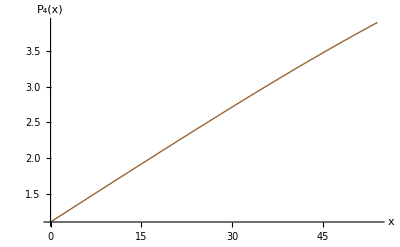

```mathematica
PlotP4=Plot[{P4[x]},{x,0,54},AxesLabel-> {"x","P_4(x)"},PlotStyle->{{Brown,Thick}}]
```

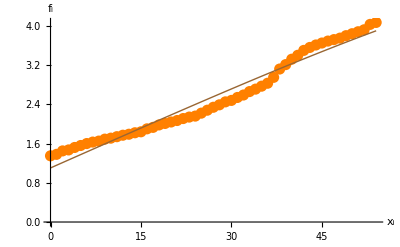

```mathematica
Show[{PlotData,PlotP4}]
```

```mathematica
fP4 = P4[xi]
```

{1.10291,1.15733,1.21174,1.26612,1.32048,1.37482,1.42913,1.48341,1.53766,1.59187,1.64604,1.70017,1.75425,1.80828,1.86226,1.91617,1.97002,2.0238,2.0775,2.13112,2.18466,2.2381,2.29145,2.34469,2.39782,2.45084,2.50373,2.55648,2.6091,2.66158,2.7139,2.76605,2.81804,2.86985,2.92147,2.9729,3.02412,3.07513,3.12591,3.17646,3.22677,3.27682,3.32662,3.37613,3.42537,3.4743,3.52294,3.57125,3.61923,3.66687,3.71416,3.76108,3.80763,3.85378,3.89954}

```mathematica
ErorP4=fi-fP4
```

{0.24709,0.222667,0.238263,0.203878,0.199516,0.185178,0.170867,0.146586,0.112339,0.0981272,0.0639555,0.0398272,0.0157463,-0.0182831,-0.0422568,-0.0761701,-0.0700184,-0.0937967,-0.0974998,-0.121122,-0.144659,-0.168103,-0.181449,-0.204691,-0.237822,-0.230836,-0.223726,-0.216484,-0.219103,-0.211577,-0.233896,-0.226054,-0.228041,-0.20985,-0.211472,-0.202898,-0.19412,-0.125127,-0.00591128,0.0335379,0.09323,0.123175,0.173384,0.183866,0.184633,0.175696,0.167065,0.148752,0.130769,0.133127,0.125838,0.118915,0.11237,0.176216,0.170465}

Berikut merupakan grafik distribusi eror dari polinomial pendekatan berderajat empat.

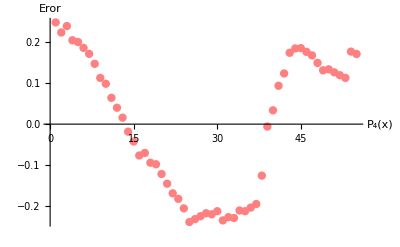

```mathematica
ploter4=ListPlot[ErorP4,PlotRange->All,PlotStyle->{Pink,PointSize[0.015]},AxesLabel->{"P_4(x)","Eror"}]
```

```mathematica
EP4=Total[wi(ErorP4)^2]
```

1.51376

Diperoleh nilai E (eror) dari polinomial pendekatan berderajat dua adalah E(P_4) = 1.51376.

Berikut merupakan grafik gabungan polinomial pendekatan diatas.

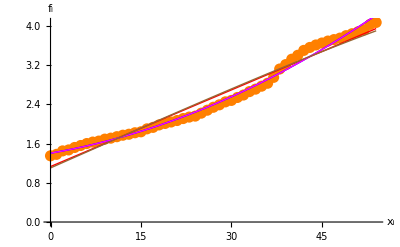

```mathematica
Show[{PlotData,PlotP1,PlotP2,PlotP3,PlotP4}]
```

Berikut merupakan grafik gabungan distribusi eror diatas.

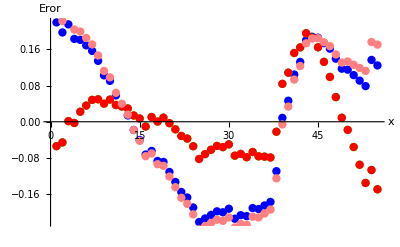

```mathematica
Show[{ploter1,ploter2,ploter3,ploter4},AxesLabel->{"x","Eror"}]
```